# Mathematica Lab 1-Properties Fourier Series Representation

## Property-Time Shifting of a Discrete-Time Periodic Signal (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *22.09.2022*

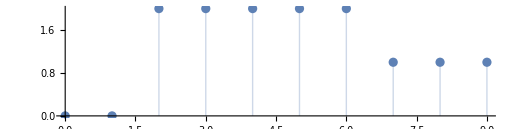

```mathematica
(* This defines one period of the periodic signal x[n]: *)
P=10;
x[n_Integer]:=Piecewise[{{0,0≤Mod[n,P]<2},{2,2≤Mod[n,P]≤6},{1,6<Mod[n,P]≤9}}];
(* This defines the period of the signal: *)(* P is the notation for big N *)
(* This plots the single period of the signal: *)
ListPlot[Table[{n,x[n]},{n,0,9}],Filling->Axis,AspectRatio->1/4]
```

1/10 (2 ⅇ^(-2/5 ⅈ k π)+2 ⅇ^(-3/5 ⅈ k π)+2 ⅇ^(-4/5 ⅈ k π)+2 ⅇ^(-ⅈ k π)+2 ⅇ^(-6/5 ⅈ k π)+ⅇ^(-7/5 ⅈ k π)+ⅇ^(-8/5 ⅈ k π)+ⅇ^(-9/5 ⅈ k π))

0 | 13/10
1 | -11/40-3/(8 √5)+ⅈ (1/10 √(5/8-(√5)/8)-1/5 √(5/8+(√5)/8))
2 | -3/40-1/(8 √5)+1/10 ⅈ √(5/8+(√5)/8)
3 | -11/40+3/(8 √5)+ⅈ (1/5 √(5/8-(√5)/8)+1/10 √(5/8+(√5)/8))
4 | -3/40+1/(8 √5)+1/10 ⅈ √(5/8-(√5)/8)
5 | 1/10
6 | -3/40+1/(8 √5)-1/10 ⅈ √(5/8-(√5)/8)
7 | -11/40+3/(8 √5)+ⅈ (-1/5 √(5/8-(√5)/8)-1/10 √(5/8+(√5)/8))
8 | -3/40-1/(8 √5)-1/10 ⅈ √(5/8+(√5)/8)
9 | -11/40-3/(8 √5)+ⅈ (-1/10 √(5/8-(√5)/8)+1/5 √(5/8+(√5)/8))

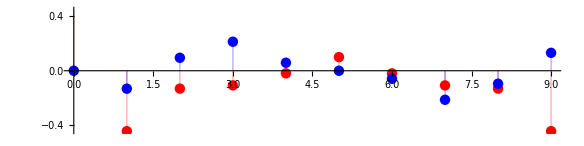

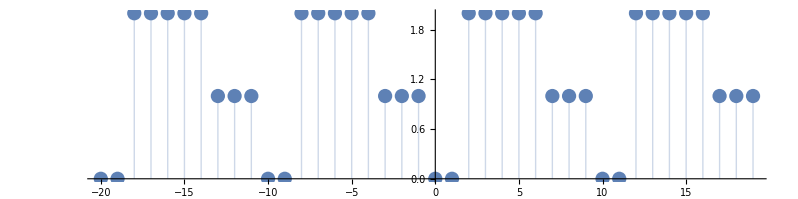

```mathematica
(* This computes the Fourier Series coefficients: *)
a[k_Integer]=1/P Total[Table[x[n]Exp[-ⅉ k (2π)/P n],{n,0,P-1}]]
(* These are all the ak's: *)
Grid[Table[{k,ComplexExpand[a[k]]},{k,0,P-1}],Frame->All]
(* This plots the real and imaginary parts of the ak's: *)
Pak=ListPlot[{Table[{k,Re[a[k]]},{k,0,P-1}],Table[{k,Im[a[k]]},{k,0,P-1}]},Filling->Axis,PlotStyle->{Red,Blue},AspectRatio->1/4]
(* This synthesizes the discrete-time signal x[n]: *)
xsyntesized[n_Integer]:=Total[Table[a[k]Exp[ⅉ k (2π)/10 n],{k,0,9}]]
(* This Plots the synthesized discrete-time signal x[n]: *)
Px=ListPlot[Table[{n,ComplexExpand[xsyntesized[n]]},{n,-20,19}],Filling->Axis,AspectRatio->1/4]
```

```mathematica
(* THIS IMPLEMENTS THE TIME SHIFTING *)
(* X[N-N0] *)
n0:=7; 
y[n_]:=x[n-n0];
```

1/10 (2+2 ⅇ^(-1/5 ⅈ k π)+2 ⅇ^(-2/5 ⅈ k π)+2 ⅇ^(-3/5 ⅈ k π)+ⅇ^(-4/5 ⅈ k π)+ⅇ^(-ⅈ k π)+ⅇ^(-6/5 ⅈ k π)+2 ⅇ^(-9/5 ⅈ k π))

0 | 13/10
1 | 3/20+1/(4 √5)-2/5 ⅈ √(5/8+(√5)/8)
2 | 1/20+1/(4 √5)
3 | 3/20-1/(4 √5)+2/5 ⅈ √(5/8-(√5)/8)
4 | 1/20-1/(4 √5)
5 | -1/10
6 | 1/20-1/(4 √5)
7 | 3/20-1/(4 √5)-2/5 ⅈ √(5/8-(√5)/8)
8 | 1/20+1/(4 √5)
9 | 3/20+1/(4 √5)+2/5 ⅈ √(5/8+(√5)/8)

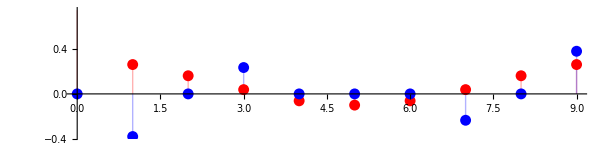

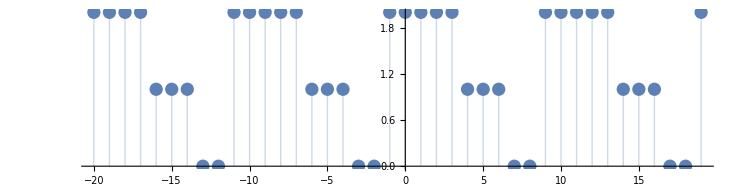

```mathematica
(* This computes the Fourier Series coefficients (the transformation is included below): : *)
b[k_Integer]=1/P Total[Table[y[n]Exp[-ⅉ k (2π)/P n],{n,0,P-1}]]
(* These are all the ak's: *)
Grid[Table[{k,ComplexExpand[b[k]]},{k,0,P-1}],Frame->All]
(* This plots the real and imaginary parts of the ak's: *)
Pbk=ListPlot[{Table[{k,Re[b[k]]},{k,0,P-1}],Table[{k,Im[b[k]]},{k,0,P-1}]},Filling->Axis,PlotStyle->{Red,Blue},AspectRatio->1/4]
(* This synthesizes the discrete-time signal x[n-n0] (the transformation is included below): *)
ysyntesized[n_Integer ]:=Total[Table[b[k]Exp[ⅉ k (2π)/10 n],{k,0,9}]]
(* This Plots the synthesized discrete-time signal x[n] *)
Py=ListPlot[Table[{n,ComplexExpand[ysyntesized[n]]},{n,-20,19}],Filling->Axis,AspectRatio->1/4]
```

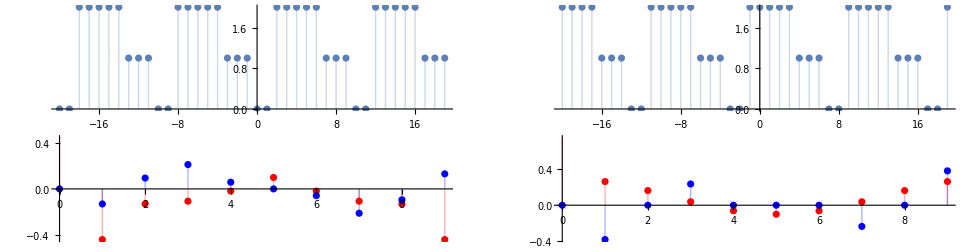

```mathematica
(* This shows all plots in one overview: *)
GraphicsGrid[{{Px,Py},{Pak,Pbk}},Frame->True]
```